```mathematica
<<init`
```

```mathematica
DSolve[x''[NN]-3x'[NN]+9/4 x[NN]==0,x[NN],NN]
```

{{x[NN]→ⅇ^(3 NN/2) C[1]+ⅇ^(3 NN/2) NN C[2]}}

```mathematica
xsol[NN_]=(xs+CC(NN-Ns))E^(3(NN-Ns)/2);
```

```mathematica
psol[NN_]=-xsol'[NN]//Simplify
```

-1/2 ⅇ^((3 (NN-Ns))/2) (CC (2+3 NN-3 Ns)+3 xs)

```mathematica
ps=psol[Ns]
```

1/2 (-2 CC-3 xs)

```mathematica
psol[NN]+3/2 xsol[NN]//Simplify
```

-CC ⅇ^((3 (NN-Ns))/2)

```mathematica
Simplify[2/3 Log[(psol[NN]+3/2 xsol[NN])/(ps+3/2 xs)],{NN-Ns>0}]
```

NN-Ns

```mathematica
2/3 Log[(pp+dp+3/2(xx+dx))/(pps+dps+3/2 xxs)]-2/3 Log[(pp+3/2 xx)/(pps+3/2 xxs)]
```

-2/3 Log[(pp+(3 xx)/2)/(pps+(3 xxs)/2)]+2/3 Log[(dp+pp+(3 (dx+xx))/2)/(dps+pps+(3 xxs)/2)]

```mathematica
Solve[{pox==psol[NN]/xsol[NN],p32x==psol[NN]+3/2 xsol[NN]},{CC,NN}]
```

$Aborted

```mathematica
Csol=CC/.Solve[p32x==psol[NN]+3/2 xsol[NN],CC][[1]]//Simplify
```

-ⅇ^(-3/2 (NN-Ns)) p32x

```mathematica
psol[NN]+3/2 xsol[NN]/.{CC->Csol}//Simplify
```

(ⅇ^((3 (NN-Ns))/2) xs-xx)/(NN-Ns)

```mathematica
Nsol=NN/.Solve[pp==psol[NN]/.{CC->Csol}//Simplify,NN][[1]]//Simplify
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

(6 Ns pp-6 xx+9 Ns xx-2 (2 pp+3 xx) ProductLog[-(3 ⅇ^(-(3 xx)/(2 pp+3 xx)) xs)/(2 pp+3 xx)])/(6 pp+9 xx)

```mathematica
pssol[xx_,pp_]=psol[Ns]/.{CC->Csol}/.{NN->Nsol}//Simplify
```

-(3 xs)/2+(3 ⅇ^(-3 Ns/2) (2 pp+3 xx) (-ⅇ^(3 Ns/2) xs+ⅇ^((6 Ns pp+6 xx+9 Ns xx+(4 pp+6 xx) ProductLog[-(3 ⅇ^(-(3 xx)/(2 pp+3 xx)) xs)/(2 pp+3 xx)])/(4 pp+6 xx)) xx))/(2 (3 xx+(2 pp+3 xx) ProductLog[-(3 ⅇ^(-(3 xx)/(2 pp+3 xx)) xs)/(2 pp+3 xx)]))

```mathematica
pssol[xx+dx,pp+dp]-pssol[xx,pp]//FunctionExpand
```

-(3 ⅇ^(-3 Ns/2) (2 pp+3 xx) (-ⅇ^(3 Ns/2) xs+ⅇ^((6 Ns pp+6 xx+9 Ns xx+(4 pp+6 xx) ProductLog[-(3 ⅇ^(-(3 xx)/(2 pp+3 xx)) xs)/(2 pp+3 xx)])/(4 pp+6 xx)) xx))/(2 (3 xx+(2 pp+3 xx) ProductLog[-(3 ⅇ^(-(3 xx)/(2 pp+3 xx)) xs)/(2 pp+3 xx)]))+(3 ⅇ^(-3 Ns/2) (2 (dp+pp)+3 (dx+xx)) (-ⅇ^(3 Ns/2) xs+ⅇ^((6 Ns (dp+pp)+6 (dx+xx)+9 Ns (dx+xx)+(4 (dp+pp)+6 (dx+xx)) ProductLog[-(3 ⅇ^(-(3 (dx+xx))/(2 (dp+pp)+3 (dx+xx))) xs)/(2 (dp+pp)+3 (dx+xx))])/(4 (dp+pp)+6 (dx+xx))) (dx+xx)))/(2 (3 (dx+xx)+(2 (dp+pp)+3 (dx+xx)) ProductLog[-(3 ⅇ^(-(3 (dx+xx))/(2 (dp+pp)+3 (dx+xx))) xs)/(2 (dp+pp)+3 (dx+xx))]))

```mathematica
PhaseV[x_,p_]={-p,3p+9/4 x};
```

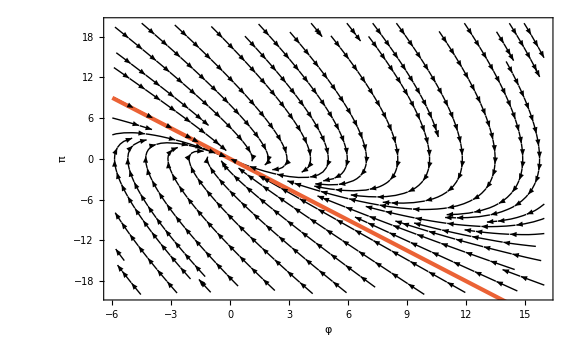

```mathematica
Show[StreamPlot[-PhaseV[x,p],{x,-6,16},{p,-20,20},AxesOrigin->{0,0},Axes->True,FrameLabel->{φ,π},PlotRange->{{-6,16},{-20,20}},StreamStyle->Black,StreamColorFunction->None],Plot[-3/2 x,{x,-6,16},PlotStyle->{Color[4],AbsoluteThickness[3]}]]
```